```mathematica
Quit[]
Clear["Global`*"]
```

Antagonistic Specialization Adaptive Dynamics. We begin by defining the change in frequency of each strategist type over time:

```mathematica
(*To begin we first define the payoffs received by hosts and symbionts*)
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*αg -> the generalist exchange rate*)
pi=x*(α−x); (*Host matched payoff*)
pi'=x*(fα−x);(*Host mis-matched payoff*)
pig=x*(αg−x);(*Generalist host payoff*)
ψ=x*(1−α);(*Symbiont matched payoff*)
ψ'=x*(1−fα);(*Host mis-matched payoff*)
ψg=x*(1−αg); (*Symbiont payoff from interaction with generalist host*)
```

```mathematica
(*v1 = frequency of host 1*)
(*v2 = frequency of host 2*)
S1 = v1*ψ+v2*ψ'+(1−v1−v2)*ψg;(*Symbiont 1 Average Payoff*)
S2 = v1*ψ'+v2*ψ+(1−v1−v2)*ψg;(*Symbiont 2 Average Payoff*)
S = u*(1-u)*(S1-S2);
S=Simplify[S]; (*Change in Symbiont Frequency over time*)
S/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

-(-1+u) u x (fα-α) (v_1-v_2)

```mathematica
(*u = frequency of symbiont 1*)
H1=u*pi+(1-u)*pi';(*Host 1 Average Payoff*)
H2 = u*pi'+(1−u)*pi;(*Host 2 Average Payoff*)
HG = pig;(*Generalist Host Average Payoff*)
Hbar = v1*H1+v2*H2+(1-v1-v2)(HG);(*Average payoff of a host selected at random*)
V1=v1*(H1-Hbar);(*Change in Host 1 frequency over time*)
V1=Simplify[V1];
V1/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
V2=v2(H2-Hbar);(*Change in Host 2 frequency over time*)
V2=Simplify[V2];
V2/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

x v_1 (fα-fα v_1+fα u (-1+v_1-v_2)-α v_2+u α (1-v_1+v_2)-α_g+v_1 α_g+v_2 α_g)

-x v_2 (α (-1+u+u v_1+v_2-u v_2)+fα (v_1+u (-1-v_1+v_2))-(-1+v_1+v_2) α_g)

First we find the equilibria of our system:

Equilibria:

```mathematica
Solve[S==0,u]
Solve[V1 ==0,v1]
Solve[V2 ==0,v2]
```

{{u→0},{u→1}}

{{v1→0},{v1→(-fα+fα u+fα u v2-u α+v2 α-u v2 α+αg-v2 αg)/(-fα+fα u-u α+αg)}}

{{v2→0},{v2→(fα u-fα v1+fα u v1+α-u α-u v1 α-αg+v1 αg)/(fα u+α-u α-αg)}}

Equilibria given as ordered triples: (u, v, p). First boundary Equilibria are the generalist equilibria: (0,0,0) and (1,0,0)

There are other boundary equilibria that occur when a given strategist is absent from the population:

```mathematica
v1s = (-fα+fα u+fα u v2-u α+v2 α-u v2 α+αg-v2 αg)/(-fα+fα u-u α+αg);
v2s = (fα u-fα v1+fα u v1+α-u α-u v1 α-αg+v1 αg)/(fα u+α-u α-αg);
Simplify[v2s /. {u -> 0, v1-> 0}]
Simplify[v2s /. {u -> 1, v1 -> 0}]
Simplify[v1s /. {u -> 0, v2 -> 0}]
Simplify[v1s /. { u -> 1, v2-> 0}]
(*Simplifying a host's internal equilibrium when two strategists are absent reveal additional boundary equilibria*)
```

1

1

1

«1 more identical outputs»

The remaining boundary equilibria are thus: 
Matched: (1,1,0) ,(0,0,1) and
Mismatched: (0,1,0)  (1,0,1)

We also considered internal host equilibria:

```mathematica
v2intu0 = Simplify[v2s /.  u-> 0];
Collect[v2intu0, v1]
v2intu1= Simplify[v2s /. u -> 1];
Collect[v2intu1, v1] 

v1intu0= Simplify[v1s /. u -> 0];
Collect[v1intu0, v2]

v1intu1= Simplify[v1s /. u -> 1];
Collect[v1intu1, v2]
```

1+(v1 (-fα+αg))/(α-αg)

1+(v1 (-α+αg))/(fα-αg)

1+(v2 (-α+αg))/(fα-αg)

1+(v2 (-fα+αg))/(α-αg)

Note the symmetry of these expressions, and that all of them violate our model’s variable constraints by resulting in a host frequency that exceeds 1.

We linearize this system by constructing the jacobian matrix:

```mathematica
J = ({{D[S,u], D[S,v1], D[S,v2]}, {D[V1,u], D[V1,v1], D[V1,v2]}, {D[V2,u], D[V2,v1], D[V2,v2]}});
```

We then evaluate the sign of eigenvalues corresponding to the jacobian evaluated at the boundary equilibria:

```mathematica
(*Generalist Equilibria*)
Eigenvalues[J/.{u -> 0,v1->  0,v2-> 0}]
Eigenvalues[J/.{u -> 1,v1->  0,v2-> 0} ] /.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

{0,x (fα-αg),x (α-αg)}

{0,x (fα-α_g),x (α-α_g)}

```mathematica
(*Matched Equilibria*)
Eigenvalues[J/.{u -> 1,v1->  1,v2-> 0} ]
Eigenvalues[J/.{u -> 0,v1->  0,v2-> 1} ]
```

{x (fα-α),x (-fα+α),x (-α+αg)}

{x (fα-α),x (-fα+α),x (-α+αg)}

```mathematica
(*Mismatched Equilibria*)
Eigenvalues[J/.{u -> 1,v1->  0,v2-> 1} ]
Eigenvalues[J/.{u -> 0,v1->  1,v2-> 0} ]
```

{x (fα-α),x (-fα+α),x (-fα+αg)}

{x (fα-α),x (-fα+α),x (-fα+αg)}

While most equilibria were found to violate model parameters when manipulated algebraically,  a sole internal equilibrium at (0.5, 0.5, 0.5) remains. We evaluated the eigenvalues at this point:

```mathematica
Eigenvalues[J/.{u -> 1/2,v1->  1/2,v2-> 1/2} ]/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

{-1/2 ⅈ x (fα-α),1/2 ⅈ x (fα-α),-1/2 x (fα+α-2 α_g)}

We used the central limit theorem to evaluate the stability of this internal saddle. We redefine variables so the center ocurs at (0,0,0):

```mathematica
F = {S, V1,V2}/.{v2 -> (v2+1/2), v1 -> (v1+1/2), u -> (u+1/2)}
JC=D[F,{{u,v1,v2}}]/.{u-> 0,v1-> 0,v2-> 0};
```

Build a transformation matrix P:

```mathematica
P= ({{0, 1, 0}, {-1, 0, 1}, {1, 0, 1}});
```

(y_1
y_2
z)= P^-1(u
v_1
v_2). We can now define the linear part of this new coordinate system, Λ:

```mathematica
Λ=Simplify[Inverse[P].JC.P];
```

Then we can build our system in block diagonal form:

```mathematica
EQ=Simplify[Λ.({{y1}, {y2}, {z}})+Inverse[P].(F-JC.({{u}, {v1}, {v2}}))/.Thread[{u,v1,v2}-> P.{y1,y2,z}]];
```

This means that the rate of change in our system may be determined as:

Next we use the centre manifold theorem to determine the stability of the higher order terms. We define z=m(y1,y2) as a series expansion.

```mathematica
m=a20*y1^2+a11*y1*y2+a30*y1^3+a21*y1^2*y2+a02*y2^2+a03*y2^3+a12*y1*y2^2+a40*y1^4+a04*y2^4+a22*y1^2*y2^2+a31*y1^3*y2+a13*y1*y2^3;
({{y1dot}, {y2dot}, {zdot}})= Λ.({{y1}, {y2}, {z}})+ϕy1y2z/.{z-> m};
```

Finally solve for the expansion coefficients of the second order expansion using the invariance condition:

```mathematica
IC=D[m,y1]*y1dot+D[m,y2]y2dot-zdot;(*=0*)
```

```mathematica
Q1=Coefficient[IC/.{y2->0},y1^2];
Q2=Coefficient[IC,y1*y2];
Q3=Coefficient[IC/.{y2->0},y1^3];
Q4=Coefficient[IC,y1^2*y2];
Q5=Coefficient[IC/.{y1->0},y2^2];
Q6=Coefficient[IC/.{y1->0},y2^3];
Q7=Coefficient[IC,y1*y2^2];
Q8=Coefficient[IC/.{y2->0},y1^4];
Q9=Coefficient[IC,y1^2*y2^2];
Q10=Coefficient[IC/.{y1->0},y2^4];
Q11=Coefficient[IC,y1^3*y2];
Q12=Coefficient[IC,y1*y2^3];
```

```mathematica
Solve[{Q1==0,Q2==0,Q3==0,Q4==0,Q5==0,Q6==0,Q7==0,Q8==0,Q9==0,Q10==0,Q11==0,Q12==0},{a11,a20,a30,a21,a02,a03,a12,a40,a04,a22,a31,a13}]
```

{{a11→0,a20→0,a30→0,a21→0,a02→0,a03→0,a12→0,a40→0,a04→0,a22→0,a31→0,a13→0}}

```mathematica
(*Inevitable because zdot is a multiple of z!*)
```

Dynamics on the center manifold are given by:

```mathematica
y1dotcm= Simplify[y1dot/.{a11->0,a20->0,a30->0,a21->0,a02->0,a03->0,a12->0,a40->0,a04->0,a22->0,a31->0,a13->0}]
y2dotcm= Simplify[y2dot/.{a11->0,a20->0,a30->0,a21->0,a02->0,a03->0,a12->0,a40->0,a04->0,a22->0,a31->0,a13->0}]
```

-1/2 x (-1+4 y1^2) y2 (fα-α)

1/2 x y1 (-1+4 y2^2) (fα-α)

Plotted as a vector field:

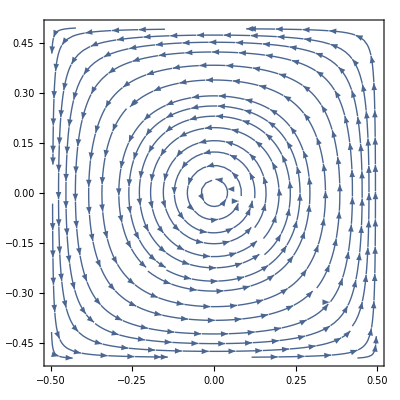

```mathematica
VF={y1dotcm,y2dotcm}/.{α->0.7,fα-> 0.5,x->0.5} ;
StreamPlot[VF,{y1,-0.5,0.5},{y2,-0.5,0.5}]
```